Note: Cells in green match the answers in the text.

Calculus.
1 to 8. Solve the ODE by integration or by remembering a differentiation formula.

1. y' + 2 sin 2πx = 0

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[y'[x] + 2 Sin[2π x]==0, y[x], x]
```

{{y[x]→C[1]+Cos[2 π x]/π}}

```mathematica
Clear["Global`*"]
```

2. y' + xe^(-x^2/2)=0

```mathematica
DSolve[y[x] + x ⅇ^(-x^2/2)==0, y[x], x]
```

{{y[x]→-ⅇ^(-x^2/2) x}}

```mathematica
Clear["Global`*"]
```

3. y' = y

```mathematica
DSolve[y'[x]==y[x],y[x],x]
```

{{y[x]→ⅇ^x C[1]}}

4. y' =-1.5y

```mathematica
DSolve[y'[x]==-1.5 y[x], y[x], x]
```

{{y[x]→ⅇ^(-1.5 x) C[1]}}

5. y' = 4ⅇ^-x cos x

```mathematica
DSolve[y'[x]==4 ⅇ^-x Cos[x], y[x], x]
```

{{y[x]→C[1]+2 ⅇ^-x (-Cos[x]+Sin[x])}}

6. y' ' = - y

```mathematica
DSolve[y''[x]==-y[x], y[x],x]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

7. y' = cosh 5.13x

```mathematica
DSolve[y'[x]==Cosh[5.13 x], y[x], x]
```

{{y[x]→C[1]+0.194932 Sinh[5.13 x]}}

```mathematica
1/5.13
```

0.194932

8. y' ' ' = ⅇ^(-0.2x)

```mathematica
DSolve[y'''[x]==ⅇ^(-0.2 x), y[x], x]
```

{{y[x]→-125. ⅇ^(-0.2 x)+C[1]+x C[2]+x^2 C[3]}}

9 to 15. Verification. Initial value problem (IVP) 
(a) Verify that y is a solution of the ODE. (b) Determine from y the particular solution of the IVP. (c) Graph the solution of the IVP.

9. y' + 4y = 1.4, y = c ⅇ^(-4x) + 0.35, y(0) = 2

```mathematica
eqn = y'[x]+4 y[x]==1.4;
sol = DSolve[eqn, y, x]
```

{{y→Function[{x},0.35+ⅇ^(-4. x) C[1]]}}

(a)

The means of checking is as follows

```mathematica
Simplify[eqn/.sol]
```

{True}

Of course if I want to go to a lot of trouble to make sure the solution in the text is really correct, I could do

```mathematica
u[x_] =(ⅇ^(-4x)+.35)
```

0.35+ⅇ^(-4 x)

```mathematica
uprime =D[ⅇ^(-4x)+.35,x]
```

-4 ⅇ^(-4 x)

```mathematica
-4 ⅇ^(-4 x)
```

-4 ⅇ^(-4 x)

```mathematica
rsec =4 u[x] + uprime
```

-4 ⅇ^(-4 x)+4 (0.35+ⅇ^(-4 x))

```mathematica
Simplify[rsec]
```

1.4

The 1.4 above is the rhs of the original equation.  The book solution checks.

(b)

```mathematica
Solve[0.35+ c1==2, c1]
```

{{c1→1.65}}

(c) In the plot below, the IVP point is seen in orange. The lower, left-most is the -0.35 line.

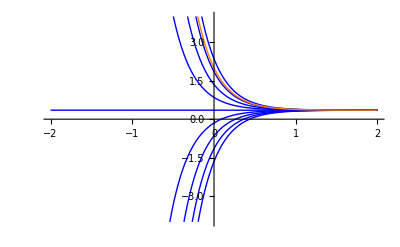

```mathematica
g[x_]=y[x]/.sol;
tab[x_]=Table[g[x]/.C[1]->j,{j,-2,2,0.5}];
tabl[x_]=Table[g[x]/.C[1]->v,{v,1.65,1.65}];Show[Plot[tab[x],{x, -2,2},PlotRange->{-4,4},PlotStyle->{Blue,Thin},GridLines->All],
Plot[tabl[x],{x, -2,2},PlotRange->{-4,4},PlotStyle->{Orange,Thick}]]
```

```mathematica
Clear["Global`*"]
```

10. y' + 5xy = 0, y = cⅇ^(-2.5 x^2), y(0) = π

```mathematica
eqn = y'[x] + 5 x y[x]==0;
sol = DSolve[eqn, y, x]
```

{{y→Function[{x},ⅇ^(-(5 x^2)/2) C[1]]}}

(a) The DSolve answer is seen to equal the book’s proposed solution.

```mathematica
Simplify[eqn/.sol]
```

{True}

(b)

```mathematica
Solve[c1==π, c1]
```

{{c1→π}}

(c)

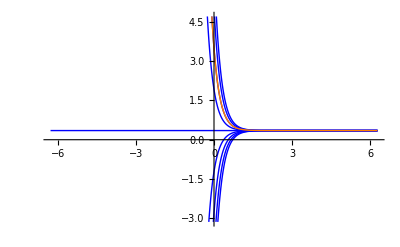

```mathematica
g[x_]=y[x]/.sol;
tab[x_]=Table[g[x]/.C[1]->j,{j,-2π,2π,π/2}];
tabl[x_]=Table[g[x]/.C[1]->v,{v,π,π}];
Show[Plot[tab[x],{x, -2π,2π},PlotRange->{-π,(3π)/2},PlotStyle->{Blue,Thin},GridLines->All],
Plot[tabl[x],{x, -2π,2π},PlotRange->{-π,(3π)/2},PlotStyle->{Orange,Thick}]]
```

```mathematica
Clear["Global`*"]
```

11. y’ = y + ⅇ^x, y = (x + c) ⅇ^x , y(0) = 1/2

```mathematica
eqn = y'[x] - y[x] - ⅇ^x == 0;
sol = DSolve[eqn, y, x]
```

{{y→Function[{x},ⅇ^x x+ⅇ^x C[1]]}}

(a) The DSolve answer is seen to equal the book’s proposed solution.

```mathematica
eqn/.sol
```

{True}

(b)

```mathematica
Solve[0 + c1 == 1/2, c1]
```

{{c1→1/2}}

(c)

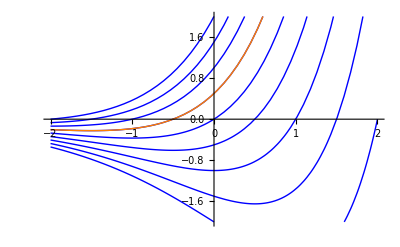

```mathematica
g[x_]=y[x]/.sol;
tab[x_]=Table[g[x]/.C[1]->j,{j,-2,2,1/2}];
tabl[x_]=Table[g[x]/.C[1]->v,{v,1/2,1/2}];
Show[Plot[tab[x],{x, -2,2},PlotRange->{-2,2},PlotStyle->{Blue,Thin},GridLines->{{0},{1/2}}],
Plot[tabl[x],{x, -2,2},PlotRange->{-2,2},PlotStyle->{Orange,Thick}]]
```

```mathematica
Clear["Global`*"]
```

12. yy’ = 4x, y^2 - 4 x^2 = C (y > 0), y(1) = 4

```mathematica
eqn = y[x] y'[x] - 4x == 0;
sol = DSolve[eqn, y, x]
```

{{y→Function[{x},-√2 √(2 x^2+C[1])]},{y→Function[{x},√2 √(2 x^2+C[1])]}}

(a) The DSolve answer [2] is seen to equal the book’s proposed solution.
i.e., for y > 0, y^2 = 4 x^2 +C ->y = √(4x^2 + C) -> √2√(2x^2 + C/Sqrt[2])

```mathematica
eqn/.sol[[2]]
```

True

(b)

```mathematica
Solve[√2 √(2 +C[1])==4, C[1]]
```

{{C[1]→6}}

(c)

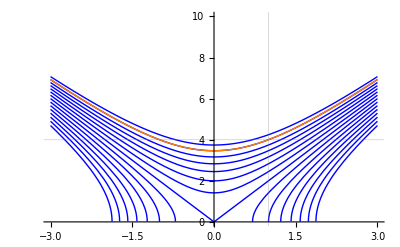

```mathematica
g[x_]=y[x]/.sol[[2]];
tab[x_]=Table[g[x]/.C[1]->j,{j,-7,7,1}];
tabl[x_]=Table[g[x]/.C[1]->v,{v,6,6}];
Show[Plot[tab[x],{x, -3,3},PlotRange->{0,10},PlotStyle->{Blue,Thin},GridLines->{{1},{4}}],
Plot[tabl[x],{x, -3,3},PlotRange->{0,10},PlotStyle->{Orange,Thick}]]
```

```mathematica
Clear["Global`*"]
```

13. y’ = y - y^2 , y = 1/(1+cⅇ^-x), y(0) = 0.25

```mathematica
eqn = y'[x] -y[x]+(y[x])^2==0;
sol = DSolve[eqn, y, x]
```

{{y→Function[{x},ⅇ^x/(ⅇ^x+ⅇ^C[1])]}}

```mathematica
Simplify[eqn]/.Simplify[sol]
```

{True}

(a)
The question is whether the following is true:
ⅇ^x/(ⅇ^x + ⅇ^C[1]) =^? 1/(1 + C[2]ⅇ^-x)
Multiplying the rhs by ⅇ^x/ⅇ^x I get:
ⅇ^x/(ⅇ^x + C[2])
So all I have to do is set C[2] = ⅇ^C[1].
Since this is legal (constants are real, not necessarily rational), I conclude that the expressions are equivalent.
(b)

```mathematica
Solve[1/(1+ⅇ^C[1])==0.25,C[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{C[1]→1.09861}}

(c)

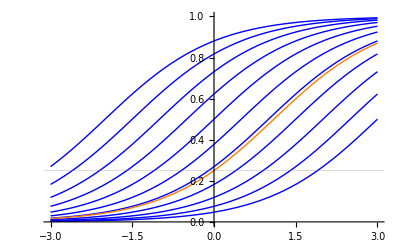

```mathematica
g[x_]=y[x]/.sol;
tab[x_]=Table[g[x]/.C[1]->j,{j,-2,3,1/2}];
tabl[x_]=Table[g[x]/.C[1]->v,{v,1.09861,1.09861}];
Show[Plot[tab[x],{x, -3,3},PlotRange->{0,1},PlotStyle->{Blue,Thin},GridLines->{{0},{0.25}}],
Plot[tabl[x],{x, -3,3},PlotRange->{0,1},PlotStyle->{Orange,Thick}]]
```

```mathematica
Clear["Global`*"]
```

14. y’ tan x = 2y + 8, y = c sin^2 x + 4, y(1/2 π) = 0

```mathematica
eqn = y'[x]Tan[x]-2 y[x]==8;
sol = DSolve[eqn, y, x]
```

{{y→Function[{x},-4 Cos[x]^2+C[1] Sin[x]^2]}}

```mathematica
Simplify[eqn/.sol]
```

{True}

(a) So the decision is whether
-4 cos^2 x + C[1] sin^2 x =^? c sin^2 x + 4.  I can get to
-4 + C[1] sin^2 x =^? c sin^2 x + 4.  However, I
don't really know the answer to that proposed equality. So I guess I better do it the long way.

```mathematica
prop1 = Sin[x]^2 + 4
```

4+Sin[x]^2

```mathematica
D[prop1, x]
```

2 Cos[x] Sin[x]

```mathematica
Simplify[(2 Cos[x] Sin[x]) Tan[x] -2 (Sin[x]^2 + 4)-8]
```

-16

It looks like Mathematica is disagreeing with the text answer.

```mathematica
Simplify[(2 Cos[x] Sin[x]) Tan[x] -2 (Sin[x]^2 - 4)-8]
```

0

(b) I don’t think this first ‘solve’ is necessary, but

```mathematica
Solve[-4 Cos[π/2]^2+C[1] Sin[π/2]^2==0, C[1]]
```

{{C[1]→0}}

```mathematica
sol2 = DSolve[{eqn, y[π/2]==0}, y, x]
```

{{y→Function[{x},-4 Cos[x]^2]}}

(c)

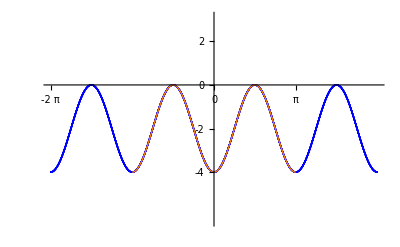

```mathematica
g[x_]=y[x]/.sol2;
tab[x_]=Table[g[x]/.C[1]->j,{j,-2,3,1/2}];
tabl[x_]=Table[g[x]/.C[1]->v,{v,0,0}];
Show[Plot[tab[x],{x, -2π,2π},PlotRange->{-2π,π},PlotStyle->{Blue,Thin},GridLines->{{π/2},{0}},Ticks->{{-2Pi, -Pi, 0,Pi/2,Pi,2Pi},{-4,-2,0,2}}],
Plot[tabl[x],{x, -π,π},PlotRange->{-2π,2π},PlotStyle->{Orange,Thick}]]
```